### Author: Tanay Roy, 13 Jun 2022

#### Common functions

```mathematica
Clear[θ,λ,itr];
OptStepG[λ_]:=Round[π/(4ArcSin[√λ])-1/2];  (* Optimal steps for Grover *)
OptStep[λ_]:=Ceiling[π/(4ArcSin[√λ])-1/2];  (* Optimal steps for D2p Grover = k *)
θopt[λ_]:=2ArcSin[1/(√λ)Sin[π/(4OptStep[λ]+2.)]]; (* Used as initial guess *)
CZ[θ_]:=({{1, 0}, {0, ⅇ^(ⅈ θ)}}); (* Grover CZ(theta) oracle *)
Gamp[θ_,λ_]:=({{1-(1-ⅇ^(ⅈ θ)) λ, (1-ⅇ^(ⅈ θ)) √(λ(1-λ))}, {(1-ⅇ^(ⅈ θ)) √(λ(1-λ)), 1-(1-ⅇ^(ⅈ θ))(1-λ)}}); (* Grover amplification step *)
G1[θ_,λ_]:=Gamp[θ,λ].CZ[θ];  (* 1 iteration of original Grover *)
DGrov1[θ_,λ_]:=Gamp[θ,λ].CZ[π];  (* 1 iteration of D2p Grover *)
```

#### Equations from D2p protocol

```mathematica
D2pEvenEq1[θ1_,θ2_, λ_]:=1+4λ (1-2 λ) Sin[θ1/2]Sin[θ2/2]  Tan[Floor[OptStep[λ]/2 ] ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2]; (* From real part of the residual amplitude *)
(* Expression for ϕ is used explicitly *)
D2pEvenEq2[θ1_,θ2_, λ_]:=(1-4λ)Tan[θ1/2]+Tan[θ2/2]; (* From imaginary part of the residual amplitude *)
D2pOddEq1[θ1_,θ2_, λ_]:=2 λ+(1-2λ) Cos[θ1]+(-1+2 λ)  Sin[θ1/2] (Cos[θ2/2] Sin[θ1]+(1+4 λ-8 λ^2+(1-8 λ+8 λ^2) Cos[θ1]) Sin[θ2/2])Tan[Floor[OptStep[λ]/2 ] ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2];
D2pOddEq2[θ1_,θ2_, λ_]:=(1-2 λ) Sin[θ1]+ (-2 λ Sin[(θ1-θ2)/2]+(-1+2 λ) (8 (-1+λ) λ Sin[θ1/2] Sin[θ1] Sin[θ2/2]-Cos[θ1] Sin[(θ1+θ2)/2])) Tan[Floor[OptStep[λ]/2 ] ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2];

D2pGsolver[λ_]:=
(* Optimal number of stapes is calculated based on λ, it is then used to compute optimal angles and then success probablity SP is determined by matrix multiplication *)
Module[{θ1,θ2},
kopt = OptStep[λ];
If[EvenQ[kopt],sol=FindRoot[{D2pEvenEq1[θ1,θ2, λ]==0,D2pEvenEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}],
sol=FindRoot[{D2pOddEq1[θ1,θ2, λ]==0,D2pOddEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}]
];
If[EvenQ[kopt],SP=((MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],kopt/2 ].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2,SP=((DGrov1[θ1,λ].MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],Floor[kopt/2 ]].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2];
vals={λ, kopt, sol[[1,2]],sol[[2,2]], SP};
Print["λ=",λ,", kopt=",kopt, ", θ_1=",sol[[1,2]], ", θ_2=",sol[[2,2]], ", SP=",SP];
vals (* Return order: λ, OptStep#, θ1val, θ2val, SuccessProb *)
]

Gsolver[λ_]:=
Module[{θ1,θ2},kopt = OptStepG[λ];
SP=((MatrixPower[G1[π,λ],kopt].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2;
vals={λ,kopt,SP}; (* Return order: λ, OptStep#, SuccessProb *)
Print["λ=",λ,", kopt=",kopt, ", SP=",SP];
vals]
```

#### From WTK1002 (Lee et al.)

```mathematica
NewEvenEq1[θ1_,θ2_, λ_]:=1+4λ (1-2 λ) Sin[θ1/2]Sin[θ2/2]  Tan[OptStep[λ]/2  ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2]; 
NewEvenEq2[θ1_,θ2_, λ_]:=(1-4λ)Tan[θ1/2]+Tan[θ2/2]; 
(* Equations for even case are identical *)
NewOddEq1[θ1_,θ2_, λ_]:=1-2λ+2Cos[θ1]λ((2-Cos[θ1]+(2Cos[θ1]-2)λ)4λ(1-2λ)Sin[θ1/2]Sin[θ2/2]-2λ Sin[θ1]Sin[(θ1-θ2)/2])Tan[(OptStep[λ]-1)/2ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2];
NewOddEq2[θ1_,θ2_, λ_]:=2λ Sin[θ1]+(2λ Cos[θ1]Sin[(θ1-θ2)/2]-4(1-2λ)^2 λ Sin[θ1]Sin[θ1/2]Sin[θ2/2]-(1-2λ)Sin[(θ1+θ2)/2])Tan[(OptStep[λ]-1)/2 ArcCos[Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2]]]/Sqrt[1-(Cos[(θ1+θ2)/2]+8λ(1-λ)Sin[θ1/2]Sin[θ2/2])^2];

NewDGsolver[λ_]:=
Module[{θ1,θ2},
kopt = OptStep[λ];
If[EvenQ[kopt],sol=FindRoot[{NewEvenEq1[θ1,θ2, λ]==0,NewEvenEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}],
sol=FindRoot[{NewOddEq1[θ1,θ2, λ]==0,NewOddEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}]
];
If[EvenQ[kopt],SP=((MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],kopt/2 ].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2,SP=((DGrov1[θ1,λ].MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],Floor[kopt/2 ]].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2];
vals={λ, kopt, sol[[1,2]],sol[[2,2]], SP};
Print["λ=",λ,", kopt=",kopt, ", θ_1=",sol[[1,2]], ", θ_2=",sol[[2,2]], ", SP=",SP];
vals (* Return order: λ, OptStep#, θ1val, θ2val, SuccessProb *)
]
```

#### Solution for λ=0.005

```mathematica
λval=0.005;
Print["Original Grover"]; Gsolver[λval];
Print["D2p protocol"]; D2pGsolver[λval];
Print["Lee et al. Grover"]; NewDGsolver[λval]; (* Numerical solution fails *)
```

Original Grover

λ=0.005, kopt=11, SP=0.996765

D2p protocol

λ=0.005, kopt=11, θ_1=2.61649, θ_2=-2.60627, SP=1.

Lee et al. Grover

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

λ=0.005, kopt=11, θ_1=1.11014, θ_2=-1.07247, SP=0.563623

#### Plot the phases for D2p

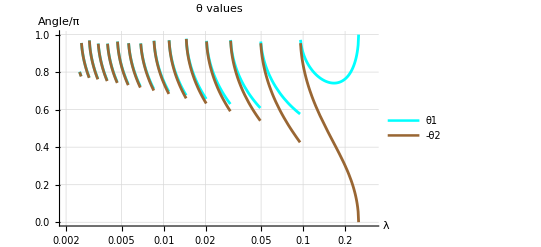

```mathematica
D2pGsolver[λ_]:=
(* Same definition as above, print statement is suppressed *)
Module[{θ1,θ2},
kopt = OptStep[λ];
If[EvenQ[kopt],sol=FindRoot[{D2pEvenEq1[θ1,θ2, λ]==0,D2pEvenEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}],
sol=FindRoot[{D2pOddEq1[θ1,θ2, λ]==0,D2pOddEq2[θ1,θ2, λ]==0},{{θ1,θopt[λ]},{θ2,-θopt[λ]}}]
];
If[EvenQ[kopt],SP=((MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],kopt/2 ].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2,SP=((DGrov1[θ1,λ].MatrixPower[DGrov1[θ2,λ].DGrov1[θ1,λ],Floor[kopt/2 ]].({{√(1-λ)}, {√λ}})/.sol//Abs)[[2,1]])^2];
vals={λ, kopt, sol[[1,2]],sol[[2,2]], SP};
(*Print["λ=",λ,", kopt=",kopt, ", θ_1=",sol[[1,2]], ", θ_2=",sol[[2,2]], ", SP=",SP];*)
vals (* Return order: λ, OptStep#, θ1val, θ2val, SuccessProb *)
]

LogLinearPlot[{D2pGsolver[λ][[3]]/π,-D2pGsolver[λ][[4]]/π},{λ,0.0025,0.25},PlotPoints->10,PlotLegends->{ "θ1","-θ2"},PlotLabel->"θ values",PlotRange->{0,1},PlotStyle->{{Cyan,Thickness[0.005]},{Brown,Thickness[0.005]}},LabelStyle->{FontFamily->"Arial",FontSize->18,Black},GridLines->Automatic,AxesLabel->{"λ","Angle/π"}]
```